Created by: jacobm on 12-20-2017 13:50:34

### Categorization

Symbol

Synonyms

### Keywords

### Syntax Templates

Details

Security Details

"   Potential security risk"

# QuantumCircuit

QuantumCircuit[{qop_1, qop_2, …}] 
yields the quantum circuit described by the ordered sequence of operations qop_i.
      QuantumCircuit[bf]
yields the reversible quantum circuit that generalizes the classical Boolean function bf from bits to qubits.

## Tutorials

Related Demonstrations

## Related Links

## See Also

## More About

Autogenerated

## Examples | More Examples ⊳

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a circuit consisting of two Pauli gates acting on the first and second subsystems respectively:

```mathematica
x = QuantumMatrixOperation["PauliX"]
```

QuantumMatrixOperation[…]

```mathematica
y=  QuantumMatrixOperation["PauliY"]
```

QuantumMatrixOperation[…]

```mathematica
circ = QuantumCircuit[{x -> {1}, y -> {2}}]
```

QuantumCircuit[…]

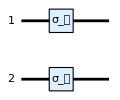

```mathematica
circ["CircuitDiagram"]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Generate a more complicated circuit, including both unitary gates and measurement of observables:

```mathematica
tl =  QuantumMatrixOperation["Toffoli"]
```

QuantumMatrixOperation[…]

```mathematica
fk =  QuantumMatrixOperation["Fredkin"]
```

QuantumMatrixOperation[…]

```mathematica
xMeas = QuantumMeasurement["Observable"->  "SigmaX"]
```

QuantumMeasurement[…]

```mathematica
circ = QuantumCircuit[{ tl -> {3, 1, 2}, fk -> {3, 2, 1}, xMeas -> {2}}]
```

QuantumCircuit[…]

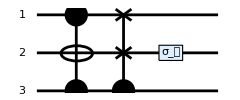

```mathematica
circ["CircuitDiagram"]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Generate a quantum circuit for an input Boolean function:

```mathematica
bf =  Xor[Or[c, b], And[a, b]]
```

(a&&b)⊻(c||b)

```mathematica
circ = QuantumCircuit["BooleanFunction" -> bf]
```

QuantumCircuit[…]

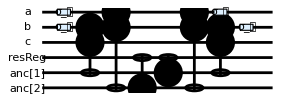

```mathematica
circ["CircuitDiagram"]
```

## More Examples

### Scope

### Properties & Relations

### Possible Issues

### Interactive Examples

### Neat Examples

Design Discussion

Application Notes

Test Cases

Function Essay